```mathematica
ExtractGraphInfo[g_Graph]:=Module[{vertices,edges,degreeOne,externalNodes},(*Get vertices*)vertices=VertexList[g];
(*Get edges as list of couples*)edges=EdgeList[g]/. {UndirectedEdge[a_,b_]:>{a,b},DirectedEdge[a_,b_]:>{a,b}};
(*Find vertices with degree 1 (external legs)*)degreeOne=Select[vertices,VertexDegree[g,#]==1&];
(*Find vertices connected to degree-1 vertices (nodes where external momenta enter)*)externalNodes=DeleteDuplicates[Flatten[Cases[edges,{a_,b_}/;MemberQ[degreeOne,a]:>b]]~Join~Flatten[Cases[edges,{a_,b_}/;MemberQ[degreeOne,b]:>a]]];
(*Return as association*)<|"Vertices"->vertices,"Edges"->edges,"Nodes"->externalNodes|>]
SortMixed[o_]:=If[!AtomQ[o],Sort[o],o]
```

```mathematica
DrawGraph[Nodes_,Edges_,Masses_]:=HighlightGraph[EdgeTaggedGraph[Join[Table[Edges⟦i,1⟧<->Edges⟦i,2⟧,{i,1,Length[Edges]}],Table[Subscript[p, i]<->Nodes⟦i⟧,{i,1,Length[Nodes]}]],VertexLabels->"Name"],Join[Table[If[!Masses⟦i⟧===0,Edges⟦i,1⟧Edges⟦i,2⟧1],{i,1,Length[Masses]}],Table[If[!Masses⟦i⟧===0,Edges⟦i,1⟧Edges⟦i,2⟧2],{i,1,Length[Masses]}],Table[If[Masses⟦i⟧===0,Style[Edges⟦i,1⟧Edges⟦i,2⟧1,Blue,Dashed]],{i,1,Length[Masses]}]]];
```

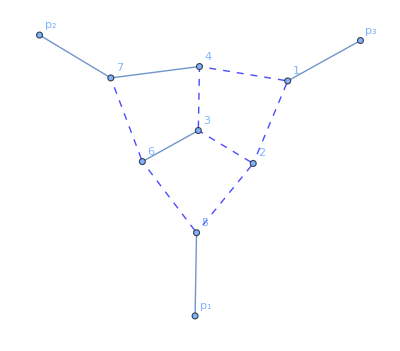
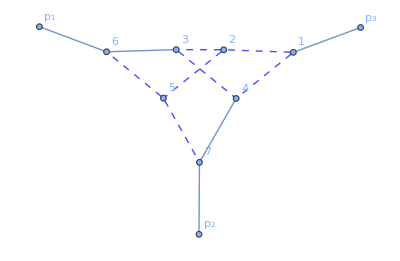
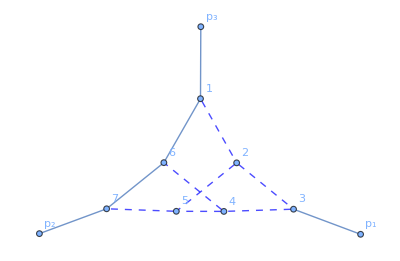
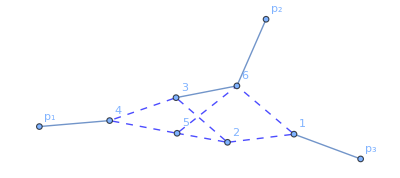
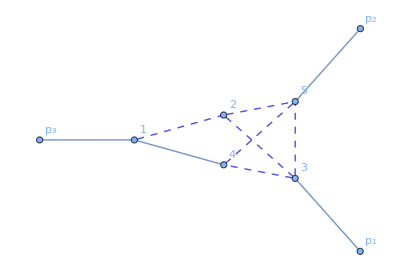

```mathematica
edges={{{1,2},{2,3},{3,4},{4,1},{2,5},{5,6},{6,7},{3,6},{4,7}},{{1,2},{2,3},{3,4},{4,1},{2,5},{5,7},{6,5},{3,6},{4,7}},{{1,2},{2,3},{3,4},{4,5},{2,5},{4,6},{7,5},{7,6},{1,6}},{{1,2},{2,3},{3,4},{4,5},{5,6},{6,1},{2,5},{3,6}},{{1,2},{2,3},{2,5},{3,4},{4,5},{3,5},{4,1}}};
vertices=DeleteDuplicates/@Flatten/@edges;
nodes={{5,7,1},{6,7,1},{3,7,1},{4,6,1},{3,5,1}};
masses={{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0}};
diagram=Table[DrawGraph[nodes[[i]],edges[[i]],masses[[i]]],{i,Length[edges]}]
kinematics={p[1]^2->0,p[2]^2->0,p[1] p[2]->1/2 r^2};
```

```mathematica
VertexEdges=Table[Table[Sum[If[edges[[j]][[k]][[1]]==vertices[[j]][[i]],e[k],If[edges[[j]][[k]][[2]]==vertices[[j]][[i]],-e[k],0]],{k,Length[edges[[j]]]}]==If[MemberQ[nodes[[j]],vertices[[j]][[i]]],p[Position[nodes[[j]],vertices[[j]][[i]]][[1,1]]],0],{i,Length[vertices[[j]]]}],{j,Length[edges]}]/. {p[3]->-p[1]-p[2]};
```

```mathematica
params=Table[Module[{nLoops=Length[edges[[q]]]-Length[vertices[[q]]]+1},Flatten[Table[Solve[Union[VertexEdges[[q]],MapIndexed[e[#1]==L[First[#2]]&,combo]],Array[e,Length[edges[[q]]]]],{combo,Subsets[Range[Length[edges[[q]]]],{nLoops}]}],1]//DeleteCases[#,{}]&],{q,Length[edges]}];
```

```mathematica
LoopLevel=3
```

3

```mathematica
Symm=Table[Thread[Array[L,LoopLevel]->#]&/@(Outer[Times,2(IntegerDigits[#,2,LoopLevel]&/@Range[0,2^LoopLevel-1]-1/2),Permutations[Array[L,LoopLevel]],1]//Flatten[#,1]&),{q,Length[edges]}];
```

```mathematica
AllDiagramIntegrands=DeleteDuplicates/@Flatten[#]&/@Table[1/Times@@(Array[e,Length[edges[[j]]]])/. params[[j]][[n]]/. Symm[[j]][[k]],{j,Length[edges]},{k,Length[Symm[[j]]]},{n,Length[params[[j]]]}]/.Thread[Array[L,LoopLevel]->{k1,k2,k3}]/.Thread[Array[p,3]->{p1,p2,p1-p2}]
```

```mathematica
Propagators= {k1^2,k2^2,k3^2,(p1-k1)^2,(p2+k1)^2,(p1-k1-k2)^2,(p2+k1+k2)^2,(p1-k1-k2-k3)^2,(p2+k1+k2+k3)^2,(p2+k2)^2,(p2+k3+k2)^2,(k2+k3)^2};
```

```mathematica
(Propagators/.{Power[x_,2]:>x})
```

{k1,k2,k3,-k1+p1,k1+p2,-k1-k2+p1,k1+k2+p2,-k1-k2-k3+p1,k1+k2+k3+p2,k2+p2,k2+k3+p2,k2+k3}

```mathematica
SortMixed/@(Propagators/.{Power[x_,2]:>x})
```

{k1,k2,k3,-k1+p1,k1+p2,-k1-k2+p1,k1+k2+p2,-k1-k2-k3+p1,k1+k2+k3+p2,k2+p2,k2+k3+p2,k2+k3}

```mathematica
Select[SortMixed/@(Table[List@@(AllDiagramIntegrands[[i]][[j]]//Denominator),{i,Length[AllDiagramIntegrands]},{j,Length[AllDiagramIntegrands[[i]]]}]//Flatten[#,1]&),SubsetQ[#,{k1+p2}]&]
```

{{k1,k2,k3,-k2+p1,-k1+k3-p2,k3-p1-p2,k2+k3-p1-p2,k1+p2,k1-k2-k3+p1+p2},{k1,k2,k3,k1+k3,-k2+p1,-k1-k2-k3+p1,k3-p1-p2,k2+k3-p1-p2,k1+p2},{k1,k2,k3,-k2-p1,-k1+k3-p2,k2+k3-p2,k3-p1-p2,k1+p2,k1-k2-k3+p2},{k1,k2,-k1-k2-k3,k3,k1+k3,-k2-p1,k2+k3-p2,k3-p1-p2,k1+p2},{k1,k2,k1+k2,k3,-k1+k3-p2,-k1-k2+k3-p2,k3-p1-p2,-k1-k2+k3-p1-p2,k1+p2},{k1,k2,k3,k1+k3,k1-k2+k3,k1-k2+k3-p1,-k1+k2-p2,k3-p1-p2,k1+p2},{k1,k2,k1+k2,k3,-k1+k3-p2,k2+k3-p2,k3-p1-p2,k2+k3-p1-p2,k1+p2},{k1,k2,k3,k1+k3,-k1+k2-p2,k2+k3-p2,k3-p1-p2,k2+k3-p1-p2,k1+p2},{k1,k2,k1+k2-k3,k3,-k2+k3,-k1-k2+p1,-k3+p1,k2-p1-p2,k1+p2},{k1,k2,k3,-k2+k3,-k3+p1,-k1+k2-k3-p2,k2-p1-p2,k1+p2,k1-k2+p1+p2},{k1,k2,k3,-k3-p1,k1+k2-k3-p1,-k1-k2+p1,-k2+k3+p1,k2-p1-p2,k1+p2},{k1,k2,k3,-k3-p1,-k2+k3+p1,k2-p1-p2,-k1+k2-k3-p1-p2,k1+p2,k1-k2+p1+p2},{k1,k2,-k1-k2-k3,k3,k1+k3,-k1-k2+p1,-k1-k2-k3+p1,k2-p1-p2,k1+p2},{k1,k2,k3,-k1+k3-p2,k2-p1-p2,k1+p2,k1-k2-k3+p2,k1-k2+p1+p2,k1-k2-k3+p1+p2},{k1,k2,k3,k1+k3,-k2+k3,-k1-k2+p1,-k2+k3+p1,k2-p1-p2,k1+p2},{k1,k2,k3,-k2+k3,-k2+k3+p1,-k1+k3-p2,k2-p1-p2,k1+p2,k1-k2+p1+p2},{k1,k2,k3,k1+k3,k1-k2+k3,-k2+p1,-k2+k3+p1,-k1+k2-k3-p1-p2,k1+p2},{k1,k2,k3,k1+k2-k3-p1,-k2+p1,-k2+k3+p1,-k1+k3-p2,-k1-k2+k3-p2,k1+p2},{k1,k2,-k2-k3,k3,k1+k3,-k2+p1,-k1-k2-k3+p1,k2+k3-p1-p2,k1+p2},{k1,k2,-k2-k3,k3,-k2+p1,-k1+k3-p2,k2+k3-p1-p2,k1+p2,k1-k2-k3+p1+p2},{k1,k2,k3,k1-k3-p1,k1+k2-k3-p1,-k2+p1,-k2+k3+p1,-k1+k3-p2,k1+p2},{k1,k2,k3,k1+k3,-k2+p1,-k2+k3+p1,-k1-k3-p1-p2,-k1+k2-k3-p1-p2,k1+p2},{k1,k2,k3,k1+k3,-k2+k3,-k2-p1,k1-k2+k3-p1,-k1+k2-k3-p2,k1+p2},{k1,k2,k1+k2-k3,k3,-k2+k3,-k2-p1,-k1+k3-p2,-k1-k2+k3-p1-p2,k1+p2},{k1,k2,-k1-k2-k3,k3,k1+k3,-k2-p1,-k2-k3-p1,k2+k3-p2,k1+p2},{k1,k2,k3,-k2-p1,-k2-k3-p1,-k1+k3-p2,k2+k3-p2,k1+p2,k1-k2-k3+p2},{k1,k2,k1+k2-k3,k3,-k2+k3,-k2-p1,k1-k3-p1,-k1+k3-p2,k1+p2},{k1,k2,k3,k1+k3,-k2+k3,-k2-p1,-k1+k2-k3-p2,-k1-k3-p1-p2,k1+p2},{k1,k2,k1+k2,-k2-k3,k3,k1-k3-p1,-k2-k3-p1,-k1+k3-p2,k1+p2},{k1,k2,-k2-k3,k3,k1+k3,-k2-k3-p1,-k1+k2-p2,-k1-k3-p1-p2,k1+p2},{k1,k2,k1+k2,k1+k2-k3,k3,k1-k3-p1,k1+k2-k3-p1,-k1+k3-p2,k1+p2},{k1,k2,k3,k1+k3,-k1+k2-p2,-k1+k2-k3-p2,-k1-k3-p1-p2,-k1+k2-k3-p1-p2,k1+p2},{k1,k2,k3,-k3+p1,-k1+k2-p2,k2-p1-p2,k2+k3-p1-p2,k1+p2,k1-k2-k3+p1+p2},{k1,k2,k1+k2,k3,-k3+p1,-k1-k2-k3+p1,k2-p1-p2,k2+k3-p1-p2,k1+p2},{k1,k2,k3,-k3-p1,-k1+k2-p2,k2+k3-p2,k2-p1-p2,k1+p2,k1-k2-k3+p2},{k1,k2,k1+k2,-k1-k2-k3,k3,-k3-p1,k2+k3-p2,k2-p1-p2,k1+p2},{k1,k2,k3,k1+k3,-k1+k2-p2,-k1+k2-k3-p2,k2-p1-p2,-k1+k2-k3-p1-p2,k1+p2},{k1,k2,k1+k2,k1+k2-k3,k3,k1+k2-k3-p1,-k1+k3-p2,k2-p1-p2,k1+p2},{k1,k2,k3,k1+k3,-k1+k2-p2,k2+k3-p2,k2-p1-p2,k2+k3-p1-p2,k1+p2},{k1,k2,k1+k2,k3,-k1+k3-p2,k2+k3-p2,k2-p1-p2,k2+k3-p1-p2,k1+p2},{k1,k2,k2-k3,k3,k1-k2+k3,-k2+p1,-k1-k3+p1,k3-p1-p2,k1+p2},{k1,k2,k2-k3,k3,-k2+p1,-k1-k2+k3-p2,k3-p1-p2,k1+p2,k1-k3+p1+p2},{k1,k2,k3,-k2-p1,k1-k2+k3-p1,-k1-k3+p1,k2-k3+p1,k3-p1-p2,k1+p2},{k1,k2,k3,-k2-p1,k2-k3+p1,k3-p1-p2,-k1-k2+k3-p1-p2,k1+p2,k1-k3+p1+p2},{k1,k2,k1+k2,-k1-k2-k3,k3,-k1-k3+p1,-k1-k2-k3+p1,k3-p1-p2,k1+p2},{k1,k2,k3,-k1+k2-p2,k3-p1-p2,k1+p2,k1-k2-k3+p2,k1-k3+p1+p2,k1-k2-k3+p1+p2},{k1,k2,k1+k2,k2-k3,k3,-k1-k3+p1,k2-k3+p1,k3-p1-p2,k1+p2},{k1,k2,k2-k3,k3,k2-k3+p1,-k1+k2-p2,k3-p1-p2,k1+p2,k1-k3+p1+p2},{k1,k2,k1+k2,k1+k2-k3,k3,-k3+p1,k2-k3+p1,-k1-k2+k3-p1-p2,k1+p2},{k1,k2,k3,k1-k2+k3-p1,-k3+p1,k2-k3+p1,-k1+k2-p2,-k1+k2-k3-p2,k1+p2},{k1,k2,k1+k2,-k2-k3,k3,-k3+p1,-k1-k2-k3+p1,k2+k3-p1-p2,k1+p2},{k1,k2,-k2-k3,k3,-k3+p1,-k1+k2-p2,k2+k3-p1-p2,k1+p2,k1-k2-k3+p1+p2},{k1,k2,k3,k1-k2-p1,k1-k2+k3-p1,-k3+p1,k2-k3+p1,-k1+k2-p2,k1+p2},{k1,k2,k1+k2,k3,-k3+p1,k2-k3+p1,-k1-k2-p1-p2,-k1-k2+k3-p1-p2,k1+p2},{k1,k2,k1+k2,k2-k3,k3,-k3-p1,k1+k2-k3-p1,-k1-k2+k3-p2,k1+p2},{k1,k2,k2-k3,k3,k1-k2+k3,-k3-p1,-k1+k2-p2,-k1+k2-k3-p1-p2,k1+p2},{k1,k2,k1+k2,-k1-k2-k3,k3,-k3-p1,-k2-k3-p1,k2+k3-p2,k1+p2},{k1,k2,k3,-k3-p1,-k2-k3-p1,-k1+k2-p2,k2+k3-p2,k1+p2,k1-k2-k3+p2},{k1,k2,k2-k3,k3,k1-k2+k3,k1-k2-p1,-k3-p1,-k1+k2-p2,k1+p2},{k1,k2,k1+k2,k2-k3,k3,-k3-p1,-k1-k2+k3-p2,-k1-k2-p1-p2,k1+p2},{k1,k2,-k2-k3,k3,k1+k3,k1-k2-p1,-k2-k3-p1,-k1+k2-p2,k1+p2},{k1,k2,k1+k2,-k2-k3,k3,-k2-k3-p1,-k1+k3-p2,-k1-k2-p1-p2,k1+p2},{k1,k2,k3,k1+k3,k1-k2+k3,k1-k2-p1,k1-k2+k3-p1,-k1+k2-p2,k1+p2},{k1,k2,k1+k2,k3,-k1+k3-p2,-k1-k2+k3-p2,-k1-k2-p1-p2,-k1-k2+k3-p1-p2,k1+p2},{k1,k2,k3,-k2+p1,-k1-k3-p2,-k3-p1-p2,k2-k3-p1-p2,k1+p2,k1-k2+k3+p1+p2},{k1,k2,k1-k3,k3,-k2+p1,-k1-k2+k3+p1,-k3-p1-p2,k2-k3-p1-p2,k1+p2},{k1,k2,k3,-k2-p1,-k1-k3-p2,k2-k3-p2,-k3-p1-p2,k1+p2,k1-k2+k3+p2},{k1,k2,k1-k3,k3,-k1-k2+k3,-k2-p1,k2-k3-p2,-k3-p1-p2,k1+p2},{k1,k2,k1+k2,k3,-k1-k3-p2,-k1-k2-k3-p2,-k3-p1-p2,-k1-k2-k3-p1-p2,k1+p2},{k1,k2,k1-k3,k1-k2-k3,k3,k1-k2-k3-p1,-k1+k2-p2,-k3-p1-p2,k1+p2},{k1,k2,k1+k2,k3,-k1-k3-p2,k2-k3-p2,-k3-p1-p2,k2-k3-p1-p2,k1+p2},{k1,k2,k1-k3,k3,-k1+k2-p2,k2-k3-p2,-k3-p1-p2,k2-k3-p1-p2,k1+p2},{k1,k2,k3,-k3+p1,-k1-k2-p2,-k2-p1-p2,-k2+k3-p1-p2,k1+p2,k1+k2-k3+p1+p2},{k1,k1-k2,k2,k3,-k3+p1,-k1+k2-k3+p1,-k2-p1-p2,-k2+k3-p1-p2,k1+p2},{k1,k2,k3,-k3-p1,-k1-k2-p2,-k2+k3-p2,-k2-p1-p2,k1+p2,k1+k2-k3+p2},{k1,k1-k2,k2,-k1+k2-k3,k3,-k3-p1,-k2+k3-p2,-k2-p1-p2,k1+p2},{k1,k2,k3,k1+k3,-k1-k2-p2,-k1-k2-k3-p2,-k2-p1-p2,-k1-k2-k3-p1-p2,k1+p2},{k1,k1-k2,k2,k1-k2-k3,k3,k1-k2-k3-p1,-k1+k3-p2,-k2-p1-p2,k1+p2},{k1,k2,k3,k1+k3,-k1-k2-p2,-k2+k3-p2,-k2-p1-p2,-k2+k3-p1-p2,k1+p2},{k1,k1-k2,k2,k3,-k1+k3-p2,-k2+k3-p2,-k2-p1-p2,-k2+k3-p1-p2,k1+p2},{k1,k2,-k2-k3,k3,k1+k2+k3,-k1-k2+p1,k3+p1,k2-p1-p2,k1+p2},{k1,k2,-k2-k3,k3,k3+p1,-k1+k2+k3-p2,k2-p1-p2,k1+p2,k1-k2+p1+p2},{k1,k2,k3,k3-p1,k1+k2+k3-p1,-k1-k2+p1,-k2-k3+p1,k2-p1-p2,k1+p2},{k1,k2,k3,k3-p1,-k2-k3+p1,k2-p1-p2,-k1+k2+k3-p1-p2,k1+p2,k1-k2+p1+p2},{k1,k2,k1-k3,k3,-k1-k2+k3,-k1-k2+p1,-k1-k2+k3+p1,k2-p1-p2,k1+p2},{k1,k2,k3,-k1-k3-p2,k2-p1-p2,k1+p2,k1-k2+k3+p2,k1-k2+p1+p2,k1-k2+k3+p1+p2},{k1,k2,k1-k3,-k2-k3,k3,-k1-k2+p1,-k2-k3+p1,k2-p1-p2,k1+p2},{k1,k2,-k2-k3,k3,-k2-k3+p1,-k1-k3-p2,k2-p1-p2,k1+p2,k1-k2+p1+p2},{k1,k2,k1-k3,k1-k2-k3,k3,-k2+p1,-k2-k3+p1,-k1+k2+k3-p1-p2,k1+p2},{k1,k2,k3,k1+k2+k3-p1,-k2+p1,-k2-k3+p1,-k1-k3-p2,-k1-k2-k3-p2,k1+p2},{k1,k2,k1-k3,k3,-k2+k3,-k2+p1,-k1-k2+k3+p1,k2-k3-p1-p2,k1+p2},{k1,k2,k3,-k2+k3,-k2+p1,-k1-k3-p2,k2-k3-p1-p2,k1+p2,k1-k2+k3+p1+p2},{k1,k2,k3,k1+k3-p1,k1+k2+k3-p1,-k2+p1,-k2-k3+p1,-k1-k3-p2,k1+p2},{k1,k2,k1-k3,k3,-k2+p1,-k2-k3+p1,-k1+k3-p1-p2,-k1+k2+k3-p1-p2,k1+p2},{k1,k2,k1-k3,-k2-k3,k3,-k2-p1,k1-k2-k3-p1,-k1+k2+k3-p2,k1+p2},{k1,k2,-k2-k3,k3,k1+k2+k3,-k2-p1,-k1-k3-p2,-k1-k2-k3-p1-p2,k1+p2},{k1,k2,k1-k3,k3,-k1-k2+k3,-k2-p1,-k2+k3-p1,k2-k3-p2,k1+p2},{k1,k2,k3,-k2-p1,-k2+k3-p1,-k1-k3-p2,k2-k3-p2,k1+p2,k1-k2+k3+p2},{k1,k2,-k2-k3,k3,k1+k2+k3,-k2-p1,k1+k3-p1,-k1-k3-p2,k1+p2},{k1,k2,k1-k3,-k2-k3,k3,-k2-p1,-k1+k2+k3-p2,-k1+k3-p1-p2,k1+p2},{k1,k2,k1+k2,k3,-k2+k3,k1+k3-p1,-k2+k3-p1,-k1-k3-p2,k1+p2},{k1,k2,k1-k3,k3,-k2+k3,-k2+k3-p1,-k1+k2-p2,-k1+k3-p1-p2,k1+p2},{k1,k2,k1+k2,k3,k1+k2+k3,k1+k3-p1,k1+k2+k3-p1,-k1-k3-p2,k1+p2},{k1,k2,k1-k3,k3,-k1+k2-p2,-k1+k2+k3-p2,-k1+k3-p1-p2,-k1+k2+k3-p1-p2,k1+p2},{k1,k2,-k2-k3,k3,k1+k2+k3,k2+p1,-k1-k3+p1,k3-p1-p2,k1+p2},{k1,k2,-k2-k3,k3,k2+p1,-k1+k2+k3-p2,k3-p1-p2,k1+p2,k1-k3+p1+p2},{k1,k2,k3,k2-p1,k1+k2+k3-p1,-k1-k3+p1,-k2-k3+p1,k3-p1-p2,k1+p2},{k1,k2,k3,k2-p1,-k2-k3+p1,k3-p1-p2,-k1+k2+k3-p1-p2,k1+p2,k1-k3+p1+p2},{k1,k1-k2,k2,-k1+k2-k3,k3,-k1-k3+p1,-k1+k2-k3+p1,k3-p1-p2,k1+p2},{k1,k2,k3,-k1-k2-p2,k3-p1-p2,k1+p2,k1+k2-k3+p2,k1-k3+p1+p2,k1+k2-k3+p1+p2},{k1,k1-k2,k2,-k2-k3,k3,-k1-k3+p1,-k2-k3+p1,k3-p1-p2,k1+p2},{k1,k2,-k2-k3,k3,-k2-k3+p1,-k1-k2-p2,k3-p1-p2,k1+p2,k1-k3+p1+p2},{k1,k1-k2,k2,k1-k2-k3,k3,-k3+p1,-k2-k3+p1,-k1+k2+k3-p1-p2,k1+p2},{k1,k2,k3,k1+k2+k3-p1,-k3+p1,-k2-k3+p1,-k1-k2-p2,-k1-k2-k3-p2,k1+p2},{k1,k1-k2,k2,k2-k3,k3,-k3+p1,-k1+k2-k3+p1,-k2+k3-p1-p2,k1+p2},{k1,k2,k2-k3,k3,-k3+p1,-k1-k2-p2,-k2+k3-p1-p2,k1+p2,k1+k2-k3+p1+p2},{k1,k2,k3,k1+k2-p1,k1+k2+k3-p1,-k3+p1,-k2-k3+p1,-k1-k2-p2,k1+p2},{k1,k1-k2,k2,k3,-k3+p1,-k2-k3+p1,-k1+k2-p1-p2,-k1+k2+k3-p1-p2,k1+p2},{k1,k1-k2,k2,-k2-k3,k3,-k3-p1,k1-k2-k3-p1,-k1+k2+k3-p2,k1+p2},{k1,k2,-k2-k3,k3,k1+k2+k3,-k3-p1,-k1-k2-p2,-k1-k2-k3-p1-p2,k1+p2},{k1,k1-k2,k2,-k1+k2-k3,k3,-k3-p1,k2-k3-p1,-k2+k3-p2,k1+p2},{k1,k2,k3,-k3-p1,k2-k3-p1,-k1-k2-p2,-k2+k3-p2,k1+p2,k1+k2-k3+p2},{k1,k2,-k2-k3,k3,k1+k2+k3,k1+k2-p1,-k3-p1,-k1-k2-p2,k1+p2},{k1,k1-k2,k2,-k2-k3,k3,-k3-p1,-k1+k2+k3-p2,-k1+k2-p1-p2,k1+p2},{k1,k2,k2-k3,k3,k1+k3,k1+k2-p1,k2-k3-p1,-k1-k2-p2,k1+p2},{k1,k1-k2,k2,k2-k3,k3,k2-k3-p1,-k1+k3-p2,-k1+k2-p1-p2,k1+p2},{k1,k2,k3,k1+k3,k1+k2+k3,k1+k2-p1,k1+k2+k3-p1,-k1-k2-p2,k1+p2},{k1,k1-k2,k2,k3,-k1+k3-p2,-k1+k2+k3-p2,-k1+k2-p1-p2,-k1+k2+k3-p1-p2,k1+p2},{k1,k2,k3,k2+p1,-k1+k3-p2,k3-p1-p2,-k2+k3-p1-p2,k1+p2,k1+k2-k3+p1+p2},{k1,k2,k3,k1+k3,k2+p1,-k1+k2-k3+p1,k3-p1-p2,-k2+k3-p1-p2,k1+p2},{k1,k2,k3,k2-p1,-k1+k3-p2,-k2+k3-p2,k3-p1-p2,k1+p2,k1+k2-k3+p2},{k1,k2,-k1+k2-k3,k3,k1+k3,k2-p1,-k2+k3-p2,k3-p1-p2,k1+p2},{k1,k1-k2,k2,k3,-k1+k3-p2,-k1+k2+k3-p2,k3-p1-p2,-k1+k2+k3-p1-p2,k1+p2},{k1,k2,k3,k1+k3,k1+k2+k3,k1+k2+k3-p1,-k1-k2-p2,k3-p1-p2,k1+p2},{k1,k1-k2,k2,k3,-k1+k3-p2,-k2+k3-p2,k3-p1-p2,-k2+k3-p1-p2,k1+p2},{k1,k2,k3,k1+k3,-k1-k2-p2,-k2+k3-p2,k3-p1-p2,-k2+k3-p1-p2,k1+p2},{k1,k2,k1-k2-k3,k3,k2+k3,-k1+k2+p1,-k3+p1,-k2-p1-p2,k1+p2},{k1,k2,k3,k2+k3,-k3+p1,-k1-k2-k3-p2,-k2-p1-p2,k1+p2,k1+k2+p1+p2},{k1,k2,k3,-k3-p1,k1-k2-k3-p1,-k1+k2+p1,k2+k3+p1,-k2-p1-p2,k1+p2},{k1,k2,k3,-k3-p1,k2+k3+p1,-k2-p1-p2,-k1-k2-k3-p1-p2,k1+p2,k1+k2+p1+p2},{k1,k2,-k1+k2-k3,k3,k1+k3,-k1+k2+p1,-k1+k2-k3+p1,-k2-p1-p2,k1+p2},{k1,k2,k3,-k1+k3-p2,-k2-p1-p2,k1+p2,k1+k2-k3+p2,k1+k2+p1+p2,k1+k2-k3+p1+p2},{k1,k2,k3,k1+k3,k2+k3,-k1+k2+p1,k2+k3+p1,-k2-p1-p2,k1+p2},{k1,k2,k3,k2+k3,k2+k3+p1,-k1+k3-p2,-k2-p1-p2,k1+p2,k1+k2+p1+p2},{k1,k2,k3,k1+k3,k1+k2+k3,k2+p1,k2+k3+p1,-k1-k2-k3-p1-p2,k1+p2},{k1,k2,k3,k1-k2-k3-p1,k2+p1,k2+k3+p1,-k1+k3-p2,-k1+k2+k3-p2,k1+p2},{k1,k2,k2-k3,k3,k1+k3,k2+p1,-k1+k2-k3+p1,-k2+k3-p1-p2,k1+p2},{k1,k2,k2-k3,k3,k2+p1,-k1+k3-p2,-k2+k3-p1-p2,k1+p2,k1+k2-k3+p1+p2},{k1,k2,k3,k1-k3-p1,k1-k2-k3-p1,k2+p1,k2+k3+p1,-k1+k3-p2,k1+p2},{k1,k2,k3,k1+k3,k2+p1,k2+k3+p1,-k1-k3-p1-p2,-k1-k2-k3-p1-p2,k1+p2},{k1,k2,k3,k1+k3,k2+k3,k2-p1,k1+k2+k3-p1,-k1-k2-k3-p2,k1+p2},{k1,k2,k1-k2-k3,k3,k2+k3,k2-p1,-k1+k3-p2,-k1+k2+k3-p1-p2,k1+p2},{k1,k2,-k1+k2-k3,k3,k1+k3,k2-p1,k2-k3-p1,-k2+k3-p2,k1+p2},{k1,k2,k3,k2-p1,k2-k3-p1,-k1+k3-p2,-k2+k3-p2,k1+p2,k1+k2-k3+p2},{k1,k2,k1-k2-k3,k3,k2+k3,k2-p1,k1-k3-p1,-k1+k3-p2,k1+p2},{k1,k2,k3,k1+k3,k2+k3,k2-p1,-k1-k2-k3-p2,-k1-k3-p1-p2,k1+p2},{k1,k1-k2,k2,k2-k3,k3,k1-k3-p1,k2-k3-p1,-k1+k3-p2,k1+p2},{k1,k2,k2-k3,k3,k1+k3,k2-k3-p1,-k1-k2-p2,-k1-k3-p1-p2,k1+p2},{k1,k1-k2,k2,k1-k2-k3,k3,k1-k3-p1,k1-k2-k3-p1,-k1+k3-p2,k1+p2},{k1,k2,k3,k1+k3,-k1-k2-p2,-k1-k2-k3-p2,-k1-k3-p1-p2,-k1-k2-k3-p1-p2,k1+p2},{k1,k2,k3,k3+p1,-k1+k2-p2,k2-p1-p2,k2-k3-p1-p2,k1+p2,k1-k2+k3+p1+p2},{k1,k2,k1+k2,k3,k3+p1,-k1-k2+k3+p1,k2-p1-p2,k2-k3-p1-p2,k1+p2},{k1,k2,k3,k3-p1,-k1+k2-p2,k2-k3-p2,k2-p1-p2,k1+p2,k1-k2+k3+p2},{k1,k2,k1+k2,k3,-k1-k2+k3,k3-p1,k2-k3-p2,k2-p1-p2,k1+p2},{k1,k2,k1-k3,k3,-k1+k2-p2,-k1+k2+k3-p2,k2-p1-p2,-k1+k2+k3-p1-p2,k1+p2},{k1,k2,k1+k2,k3,k1+k2+k3,k1+k2+k3-p1,-k1-k3-p2,k2-p1-p2,k1+p2},{k1,k2,k1-k3,k3,-k1+k2-p2,k2-k3-p2,k2-p1-p2,k2-k3-p1-p2,k1+p2},{k1,k2,k1+k2,k3,-k1-k3-p2,k2-k3-p2,k2-p1-p2,k2-k3-p1-p2,k1+p2},{k1,k2,k1-k2-k3,k3,k2+k3,-k2+p1,-k1+k3+p1,-k3-p1-p2,k1+p2},{k1,k2,k3,k2+k3,-k2+p1,-k1-k2-k3-p2,-k3-p1-p2,k1+p2,k1+k3+p1+p2},{k1,k2,k3,-k2-p1,k1-k2-k3-p1,-k1+k3+p1,k2+k3+p1,-k3-p1-p2,k1+p2},{k1,k2,k3,-k2-p1,k2+k3+p1,-k3-p1-p2,-k1-k2-k3-p1-p2,k1+p2,k1+k3+p1+p2},{k1,k2,k1+k2,k3,-k1-k2+k3,-k1+k3+p1,-k1-k2+k3+p1,-k3-p1-p2,k1+p2},{k1,k2,k3,-k1+k2-p2,-k3-p1-p2,k1+p2,k1-k2+k3+p2,k1+k3+p1+p2,k1-k2+k3+p1+p2},{k1,k2,k1+k2,k3,k2+k3,-k1+k3+p1,k2+k3+p1,-k3-p1-p2,k1+p2},{k1,k2,k3,k2+k3,k2+k3+p1,-k1+k2-p2,-k3-p1-p2,k1+p2,k1+k3+p1+p2},{k1,k2,k1+k2,k3,k1+k2+k3,k3+p1,k2+k3+p1,-k1-k2-k3-p1-p2,k1+p2},{k1,k2,k3,k1-k2-k3-p1,k3+p1,k2+k3+p1,-k1+k2-p2,-k1+k2+k3-p2,k1+p2},{k1,k2,k1+k2,k3,-k2+k3,k3+p1,-k1-k2+k3+p1,k2-k3-p1-p2,k1+p2},{k1,k2,k3,-k2+k3,k3+p1,-k1+k2-p2,k2-k3-p1-p2,k1+p2,k1-k2+k3+p1+p2},{k1,k2,k3,k1-k2-p1,k1-k2-k3-p1,k3+p1,k2+k3+p1,-k1+k2-p2,k1+p2},{k1,k2,k1+k2,k3,k3+p1,k2+k3+p1,-k1-k2-p1-p2,-k1-k2-k3-p1-p2,k1+p2},{k1,k2,k1+k2,k3,k2+k3,k3-p1,k1+k2+k3-p1,-k1-k2-k3-p2,k1+p2},{k1,k2,k1-k2-k3,k3,k2+k3,k3-p1,-k1+k2-p2,-k1+k2+k3-p1-p2,k1+p2},{k1,k2,k1+k2,k3,-k1-k2+k3,k3-p1,-k2+k3-p1,k2-k3-p2,k1+p2},{k1,k2,k3,k3-p1,-k2+k3-p1,-k1+k2-p2,k2-k3-p2,k1+p2,k1-k2+k3+p2},{k1,k2,k1-k2-k3,k3,k2+k3,k1-k2-p1,k3-p1,-k1+k2-p2,k1+p2},{k1,k2,k1+k2,k3,k2+k3,k3-p1,-k1-k2-k3-p2,-k1-k2-p1-p2,k1+p2},{k1,k2,k1-k3,k3,-k2+k3,k1-k2-p1,-k2+k3-p1,-k1+k2-p2,k1+p2},{k1,k2,k1+k2,k3,-k2+k3,-k2+k3-p1,-k1-k3-p2,-k1-k2-p1-p2,k1+p2},{k1,k2,k1-k3,k1-k2-k3,k3,k1-k2-p1,k1-k2-k3-p1,-k1+k2-p2,k1+p2},{k1,k2,k1+k2,k3,-k1-k3-p2,-k1-k2-k3-p2,-k1-k2-p1-p2,-k1-k2-k3-p1-p2,k1+p2},{k1,k2,k3,k2+p1,-k1-k3-p2,-k3-p1-p2,-k2-k3-p1-p2,k1+p2,k1+k2+k3+p1+p2},{k1,k2,k1-k3,k3,k2+p1,-k1+k2+k3+p1,-k3-p1-p2,-k2-k3-p1-p2,k1+p2},{k1,k2,k3,k2-p1,-k1-k3-p2,-k2-k3-p2,-k3-p1-p2,k1+p2,k1+k2+k3+p2},{k1,k2,k1-k3,k3,-k1+k2+k3,k2-p1,-k2-k3-p2,-k3-p1-p2,k1+p2},{k1,k1-k2,k2,k3,-k1-k3-p2,-k1+k2-k3-p2,-k3-p1-p2,-k1+k2-k3-p1-p2,k1+p2},{k1,k2,k1-k3,k1+k2-k3,k3,k1+k2-k3-p1,-k1-k2-p2,-k3-p1-p2,k1+p2},{k1,k1-k2,k2,k3,-k1-k3-p2,-k2-k3-p2,-k3-p1-p2,-k2-k3-p1-p2,k1+p2},{k1,k2,k1-k3,k3,-k1-k2-p2,-k2-k3-p2,-k3-p1-p2,-k2-k3-p1-p2,k1+p2},{k1,k2,k3,k3+p1,-k1-k2-p2,-k2-p1-p2,-k2-k3-p1-p2,k1+p2,k1+k2+k3+p1+p2},{k1,k1-k2,k2,k3,k3+p1,-k1+k2+k3+p1,-k2-p1-p2,-k2-k3-p1-p2,k1+p2},{k1,k2,k3,k3-p1,-k1-k2-p2,-k2-k3-p2,-k2-p1-p2,k1+p2,k1+k2+k3+p2},{k1,k1-k2,k2,k3,-k1+k2+k3,k3-p1,-k2-k3-p2,-k2-p1-p2,k1+p2},{k1,k2,k1-k3,k3,-k1-k2-p2,-k1-k2+k3-p2,-k2-p1-p2,-k1-k2+k3-p1-p2,k1+p2},{k1,k1-k2,k2,k3,k1-k2+k3,k1-k2+k3-p1,-k1-k3-p2,-k2-p1-p2,k1+p2},{k1,k2,k1-k3,k3,-k1-k2-p2,-k2-k3-p2,-k2-p1-p2,-k2-k3-p1-p2,k1+p2},{k1,k1-k2,k2,k3,-k1-k3-p2,-k2-k3-p2,-k2-p1-p2,-k2-k3-p1-p2,k1+p2},{k1,k2,k2-k3,k3,k1-k2+k3,-k1+k2+p1,k3+p1,-k2-p1-p2,k1+p2},{k1,k2,k2-k3,k3,k3+p1,-k1-k2+k3-p2,-k2-p1-p2,k1+p2,k1+k2+p1+p2},{k1,k2,k3,k3-p1,k1-k2+k3-p1,-k1+k2+p1,k2-k3+p1,-k2-p1-p2,k1+p2},{k1,k2,k3,k3-p1,k2-k3+p1,-k2-p1-p2,-k1-k2+k3-p1-p2,k1+p2,k1+k2+p1+p2},{k1,k2,k1-k3,k3,-k1+k2+k3,-k1+k2+p1,-k1+k2+k3+p1,-k2-p1-p2,k1+p2},{k1,k2,k3,-k1-k3-p2,-k2-p1-p2,k1+p2,k1+k2+k3+p2,k1+k2+p1+p2,k1+k2+k3+p1+p2},{k1,k2,k1-k3,k2-k3,k3,-k1+k2+p1,k2-k3+p1,-k2-p1-p2,k1+p2},{k1,k2,k2-k3,k3,k2-k3+p1,-k1-k3-p2,-k2-p1-p2,k1+p2,k1+k2+p1+p2},{k1,k2,k1-k3,k1+k2-k3,k3,k2+p1,k2-k3+p1,-k1-k2+k3-p1-p2,k1+p2},{k1,k2,k3,k1-k2+k3-p1,k2+p1,k2-k3+p1,-k1-k3-p2,-k1+k2-k3-p2,k1+p2},{k1,k2,k1-k3,k3,k2+k3,k2+p1,-k1+k2+k3+p1,-k2-k3-p1-p2,k1+p2},{k1,k2,k3,k2+k3,k2+p1,-k1-k3-p2,-k2-k3-p1-p2,k1+p2,k1+k2+k3+p1+p2},{k1,k2,k3,k1+k3-p1,k1-k2+k3-p1,k2+p1,k2-k3+p1,-k1-k3-p2,k1+p2},{k1,k2,k1-k3,k3,k2+p1,k2-k3+p1,-k1+k3-p1-p2,-k1-k2+k3-p1-p2,k1+p2},{k1,k2,k1-k3,k2-k3,k3,k2-p1,k1+k2-k3-p1,-k1-k2+k3-p2,k1+p2},{k1,k2,k2-k3,k3,k1-k2+k3,k2-p1,-k1-k3-p2,-k1+k2-k3-p1-p2,k1+p2},{k1,k2,k1-k3,k3,-k1+k2+k3,k2-p1,k2+k3-p1,-k2-k3-p2,k1+p2},{k1,k2,k3,k2-p1,k2+k3-p1,-k1-k3-p2,-k2-k3-p2,k1+p2,k1+k2+k3+p2},{k1,k2,k2-k3,k3,k1-k2+k3,k2-p1,k1+k3-p1,-k1-k3-p2,k1+p2},{k1,k2,k1-k3,k2-k3,k3,k2-p1,-k1-k2+k3-p2,-k1+k3-p1-p2,k1+p2},{k1,k1-k2,k2,k3,k2+k3,k1+k3-p1,k2+k3-p1,-k1-k3-p2,k1+p2},{k1,k2,k1-k3,k3,k2+k3,k2+k3-p1,-k1-k2-p2,-k1+k3-p1-p2,k1+p2},{k1,k1-k2,k2,k3,k1-k2+k3,k1+k3-p1,k1-k2+k3-p1,-k1-k3-p2,k1+p2},{k1,k2,k1-k3,k3,-k1-k2-p2,-k1-k2+k3-p2,-k1+k3-p1-p2,-k1-k2+k3-p1-p2,k1+p2},{k1,k2,k1+k2-k3,k3,-k2+k3,k2+p1,-k1+k3+p1,-k3-p1-p2,k1+p2},{k1,k2,k3,-k2+k3,k2+p1,-k1+k2-k3-p2,-k3-p1-p2,k1+p2,k1+k3+p1+p2},{k1,k2,k3,k2-p1,k1+k2-k3-p1,-k1+k3+p1,-k2+k3+p1,-k3-p1-p2,k1+p2},{k1,k2,k3,k2-p1,-k2+k3+p1,-k3-p1-p2,-k1+k2-k3-p1-p2,k1+p2,k1+k3+p1+p2},{k1,k1-k2,k2,k3,-k1+k2+k3,-k1+k3+p1,-k1+k2+k3+p1,-k3-p1-p2,k1+p2},{k1,k2,k3,-k1-k2-p2,-k3-p1-p2,k1+p2,k1+k2+k3+p2,k1+k3+p1+p2,k1+k2+k3+p1+p2},{k1,k1-k2,k2,k3,-k2+k3,-k1+k3+p1,-k2+k3+p1,-k3-p1-p2,k1+p2},{k1,k2,k3,-k2+k3,-k2+k3+p1,-k1-k2-p2,-k3-p1-p2,k1+p2,k1+k3+p1+p2},{k1,k1-k2,k2,k3,k1-k2+k3,k3+p1,-k2+k3+p1,-k1+k2-k3-p1-p2,k1+p2},{k1,k2,k3,k1+k2-k3-p1,k3+p1,-k2+k3+p1,-k1-k2-p2,-k1-k2+k3-p2,k1+p2},{k1,k1-k2,k2,k3,k2+k3,k3+p1,-k1+k2+k3+p1,-k2-k3-p1-p2,k1+p2},{k1,k2,k3,k2+k3,k3+p1,-k1-k2-p2,-k2-k3-p1-p2,k1+p2,k1+k2+k3+p1+p2},{k1,k2,k3,k1+k2-p1,k1+k2-k3-p1,k3+p1,-k2+k3+p1,-k1-k2-p2,k1+p2},{k1,k1-k2,k2,k3,k3+p1,-k2+k3+p1,-k1+k2-p1-p2,-k1+k2-k3-p1-p2,k1+p2},{k1,k1-k2,k2,k3,-k2+k3,k3-p1,k1-k2+k3-p1,-k1+k2-k3-p2,k1+p2},{k1,k2,k1+k2-k3,k3,-k2+k3,k3-p1,-k1-k2-p2,-k1-k2+k3-p1-p2,k1+p2},{k1,k1-k2,k2,k3,-k1+k2+k3,k3-p1,k2+k3-p1,-k2-k3-p2,k1+p2},{k1,k2,k3,k3-p1,k2+k3-p1,-k1-k2-p2,-k2-k3-p2,k1+p2,k1+k2+k3+p2},{k1,k2,k1+k2-k3,k3,-k2+k3,k1+k2-p1,k3-p1,-k1-k2-p2,k1+p2},{k1,k1-k2,k2,k3,-k2+k3,k3-p1,-k1+k2-k3-p2,-k1+k2-p1-p2,k1+p2},{k1,k2,k1-k3,k3,k2+k3,k1+k2-p1,k2+k3-p1,-k1-k2-p2,k1+p2},{k1,k1-k2,k2,k3,k2+k3,k2+k3-p1,-k1-k3-p2,-k1+k2-p1-p2,k1+p2},{k1,k2,k1-k3,k1+k2-k3,k3,k1+k2-p1,k1+k2-k3-p1,-k1-k2-p2,k1+p2},{k1,k1-k2,k2,k3,-k1-k3-p2,-k1+k2-k3-p2,-k1+k2-p1-p2,-k1+k2-k3-p1-p2,k1+p2}}

```mathematica
Select[SortMixed/@(Table[List@@(AllDiagramIntegrands[[i]][[j]]//Denominator),{i,Length[AllDiagramIntegrands]},{j,Length[AllDiagramIntegrands[[i]]]}]//Flatten[#,1]&),IntersectingQ[SortMixed/@(Propagators/.{Power[x_,2]:>x}),#]&]
```

```mathematica
Select[Sort/@(Table[List@@(AllDiagramIntegrands[[i]][[j]]//Denominator),{i,Length[AllDiagramIntegrands]},{j,Length[AllDiagramIntegrands[[i]]]}]//Flatten[#,1]&),MemberQ[#]&]
```

```mathematica
Sort/@(Table[List@@(AllDiagramIntegrands[[i]][[j]]//Denominator),{i,Length[AllDiagramIntegrands]},{j,Length[AllDiagramIntegrands[[i]]]}]//Flatten[#,1]&)
```